```mathematica
parse[s_]:=ToExpression@StringReplace[s,"e"->"*^"]
```

```mathematica
readq[file_]:=Module[{rawdata,xlow,step,data,nx},
rawdata=StringSplit/@StringSplit[Import[file],"\n"];
xlow=parse@rawdata[[4,1]];
step=parse@rawdata[[5,1]];
data=Map[parse,rawdata[[7;;]],{2}];
nx=Length@data;
<|
x->(Range@nx-1/2)*step+xlow,
h->data[[All,1]],
hu->data[[All,2]],
hv->data[[All,3]]
|>
]
readbath[file_]:=Module[{rawdata,xlow,step,data,nx},
rawdata=StringSplit/@StringSplit[Import[file],"\n"];
data=Map[parse,rawdata[[7;;]],{2}];
nx=Length@data;
data[[All,-1]]
]
```

```mathematica
bath=readbath["\\\\Ubuntu\\claw_results\\_output\\fort.ref.a0000"];
qRef1=readq["\\\\Ubuntu\\claw_results\\_output\\fort.ref.q0001"];
qRef2=readq["\\\\Ubuntu\\claw_results\\_output\\fort.ref.q0002"];
qRef5=readq["\\\\Ubuntu\\claw_results\\_output\\fort.ref.q0005"];
qRef10=readq["\\\\Ubuntu\\claw_results\\_output\\fort.ref.q0010"];
```

```mathematica
bathLow=readbath["\\\\Ubuntu\\claw_results\\_output\\fort.low.a0000"];
```

```mathematica
qUnb1=readq["\\\\Ubuntu\\claw_results\\_output\\fort.unb.q0001"];
qUnb2=readq["\\\\Ubuntu\\claw_results\\_output\\fort.unb.q0002"];
qUnb5=readq["\\\\Ubuntu\\claw_results\\_output\\fort.unb.q0005"];
qUnb10=readq["\\\\Ubuntu\\claw_results\\_output\\fort.unb.q0010"];
```

```mathematica
qLev1=readq["\\\\Ubuntu\\claw_results\\_output\\fort.lev.q0001"];
qLev2=readq["\\\\Ubuntu\\claw_results\\_output\\fort.lev.q0002"];
qLev5=readq["\\\\Ubuntu\\claw_results\\_output\\fort.lev.q0005"];
qLev10=readq["\\\\Ubuntu\\claw_results\\_output\\fort.lev.q0010"];
```

```mathematica
qRog1=readq["\\\\Ubuntu\\claw_results\\_output\\fort.rog.q0001"];
qRog2=readq["\\\\Ubuntu\\claw_results\\_output\\fort.rog.q0002"];
qRog5=readq["\\\\Ubuntu\\claw_results\\_output\\fort.rog.q0005"];
qRog10=readq["\\\\Ubuntu\\claw_results\\_output\\fort.rog.q0010"];
```

```mathematica
qRogG1=readq["\\\\Ubuntu\\claw_results\\_output\\fort.q0001"];
qRogG2=readq["\\\\Ubuntu\\claw_results\\_output\\fort.q0002"];
qRogG5=readq["\\\\Ubuntu\\claw_results\\_output\\fort.q0005"];
qRogG10=readq["\\\\Ubuntu\\claw_results\\_output\\fort.q0010"];
```

```mathematica
xlow=-0.5
```

-0.5

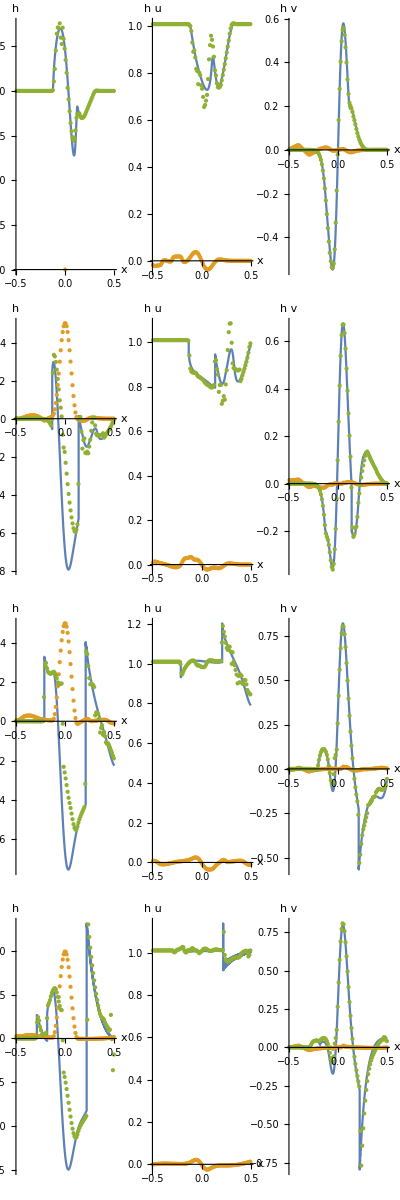

```mathematica
GraphicsGrid[#,ImageSize->1200]&/@List/@{
{
ListPlot[{Transpose[{qRef1[x],qRef1[h]+bath}],{{0,0}},Transpose[{qLev1[x],qLev1[h]+bathLow}]},hOpts={AxesOrigin->{xlow,0},Joined->{True,False,False,False,False},PlotStyle->{,PointSize@Medium,PointSize@Medium,PointSize@Medium,PointSize@Medium},AxesLabel->{Style[x,Directive@14],Style[h,Directive@14]},TicksStyle->Directive[14],PlotRange->All}],
ListPlot[{Transpose[{qRef1[x],qRef1[hu]}],{{0,0}},Transpose[{qLev1[x],qLev1[hu]}]},huOpts={AxesOrigin->{xlow,0},Joined->{True,False,False,False,False},PlotStyle->{,PointSize@Medium,PointSize@Medium,PointSize@Medium,PointSize@Medium},AxesLabel->{Style[x,Directive@14],Style[h u,Directive@14]},TicksStyle->Directive[14],PlotRange->All}],
ListPlot[{Transpose[{qRef1[x],qRef1[hv]-500(0.5Exp[-128(qRef1[x]+0.00005)^2]-0.5Exp[-128(qRef1[x]-0.00005)^2])(2+0.5Exp[-128(qRef1[x]+0.00005)^2]+0.5Exp[-128(qRef1[x]-0.00005)^2])}],{{0,0}},Transpose[{qLev1[x],qLev1[hv]-5(0.5Exp[-128(qUnb1[x]+0.005)^2]-0.5Exp[-128(qUnb1[x]-0.005)^2])(2+0.5Exp[-128(qUnb1[x]+0.005)^2]+0.5Exp[-128(qUnb1[x]-0.005)^2])}]},hvOpts={AxesOrigin->{xlow,0},Joined->{True,False,False,False,False},PlotStyle->{,PointSize@Medium,PointSize@Medium,PointSize@Medium,PointSize@Medium},AxesLabel->{Style[x,Directive@14],Style[h v,Directive@14]},TicksStyle->Directive[14],PlotRange->All}]
},
{
ListPlot[{Transpose[{qRef2[x],qRef2[h]-1-(0.5Exp[-128(qRef1[x]-0.00005)^2]+0.5Exp[-128(qRef1[x]+0.00005)^2])/2}],Transpose[{qUnb1[x],qUnb2[h]+bathLow-1-(0.5Exp[-128(qUnb1[x]-0.005)^2]+0.5Exp[-128(qUnb1[x]+0.005)^2])/2}],Transpose[{qLev2[x],qLev2[h]+bathLow-1-(0.5Exp[-128(qUnb1[x]-0.005)^2]+0.5Exp[-128(qUnb1[x]+0.005)^2])/2}]},hOpts],
ListPlot[{Transpose[{qRef2[x],qRef2[hu]}],Transpose[{qUnb1[x],qUnb2[hu]}],Transpose[{qLev2[x],qLev2[hu]}]},huOpts],
ListPlot[{Transpose[{qRef2[x],qRef2[hv]-500(0.5Exp[-128(qRef1[x]+0.00005)^2]-0.5Exp[-128(qRef1[x]-0.00005)^2])(2+0.5Exp[-128(qRef1[x]+0.00005)^2]+0.5Exp[-128(qRef1[x]-0.00005)^2])}],Transpose[{qUnb1[x],qUnb2[hv]-5(0.5Exp[-128(qUnb1[x]+0.005)^2]-0.5Exp[-128(qUnb1[x]-0.005)^2])(2+0.5Exp[-128(qUnb1[x]+0.005)^2]+0.5Exp[-128(qUnb1[x]-0.005)^2])}],Transpose[{qLev2[x],qLev2[hv]-5(0.5Exp[-128(qUnb1[x]+0.005)^2]-0.5Exp[-128(qUnb1[x]-0.005)^2])(2+0.5Exp[-128(qUnb1[x]+0.005)^2]+0.5Exp[-128(qUnb1[x]-0.005)^2])}]},hvOpts]
},
{
ListPlot[{Transpose[{qRef5[x],qRef5[h]-1-(0.5Exp[-128(qRef1[x]-0.00005)^2]+0.5Exp[-128(qRef1[x]+0.00005)^2])/2}],Transpose[{qUnb1[x],qUnb5[h]+bathLow-1-(0.5Exp[-128(qUnb1[x]-0.005)^2]+0.5Exp[-128(qUnb1[x]+0.005)^2])/2}],Transpose[{qLev5[x],qLev5[h]+bathLow-1-(0.5Exp[-128(qUnb1[x]-0.005)^2]+0.5Exp[-128(qUnb1[x]+0.005)^2])/2}]},hOpts],
ListPlot[{Transpose[{qRef5[x],qRef5[hu]}],Transpose[{qUnb1[x],qUnb5[hu]}],Transpose[{qLev5[x],qLev5[hu]}]},huOpts],
ListPlot[{Transpose[{qRef5[x],qRef5[hv]-500(0.5Exp[-128(qRef1[x]+0.00005)^2]-0.5Exp[-128(qRef1[x]-0.00005)^2])(2+0.5Exp[-128(qRef1[x]+0.00005)^2]+0.5Exp[-128(qRef1[x]-0.00005)^2])}],Transpose[{qUnb1[x],qUnb5[hv]-5(0.5Exp[-128(qUnb1[x]+0.005)^2]-0.5Exp[-128(qUnb1[x]-0.005)^2])(2+0.5Exp[-128(qUnb1[x]+0.005)^2]+0.5Exp[-128(qUnb1[x]-0.005)^2])}],Transpose[{qLev5[x],qLev5[hv]-5(0.5Exp[-128(qUnb1[x]+0.005)^2]-0.5Exp[-128(qUnb1[x]-0.005)^2])(2+0.5Exp[-128(qUnb1[x]+0.005)^2]+0.5Exp[-128(qUnb1[x]-0.005)^2])}]},hvOpts]
},
{
ListPlot[{Transpose[{qRef10[x],qRef10[h]-1-(0.5Exp[-128(qRef1[x]-0.00005)^2]+0.5Exp[-128(qRef1[x]+0.00005)^2])/2}],Transpose[{qUnb1[x],qUnb10[h]+bathLow-1-(0.5Exp[-128(qUnb1[x]-0.005)^2]+0.5Exp[-128(qUnb1[x]+0.005)^2])/2}],Transpose[{qLev10[x],qLev10[h]+bathLow-1-(0.5Exp[-128(qUnb1[x]-0.005)^2]+0.5Exp[-128(qUnb1[x]+0.005)^2])/2}]},hOpts],
ListPlot[{Transpose[{qRef10[x],qRef10[hu]}],Transpose[{qUnb1[x],qUnb10[hu]}],Transpose[{qLev10[x],qLev10[hu]}]},huOpts],
ListPlot[{Transpose[{qRef10[x],qRef10[hv]-500(0.5Exp[-128(qRef1[x]+0.00005)^2]-0.5Exp[-128(qRef1[x]-0.00005)^2])(2+0.5Exp[-128(qRef1[x]+0.00005)^2]+0.5Exp[-128(qRef1[x]-0.00005)^2])}],Transpose[{qUnb1[x],qUnb10[hv]-5(0.5Exp[-128(qUnb1[x]+0.005)^2]-0.5Exp[-128(qUnb1[x]-0.005)^2])(2+0.5Exp[-128(qUnb1[x]+0.005)^2]+0.5Exp[-128(qUnb1[x]-0.005)^2])}],Transpose[{qLev10[x],qLev10[hv]-5(0.5Exp[-128(qUnb1[x]+0.005)^2]-0.5Exp[-128(qUnb1[x]-0.005)^2])(2+0.5Exp[-128(qUnb1[x]+0.005)^2]+0.5Exp[-128(qUnb1[x]-0.005)^2])}]},hvOpts]
}
}//TableForm
```

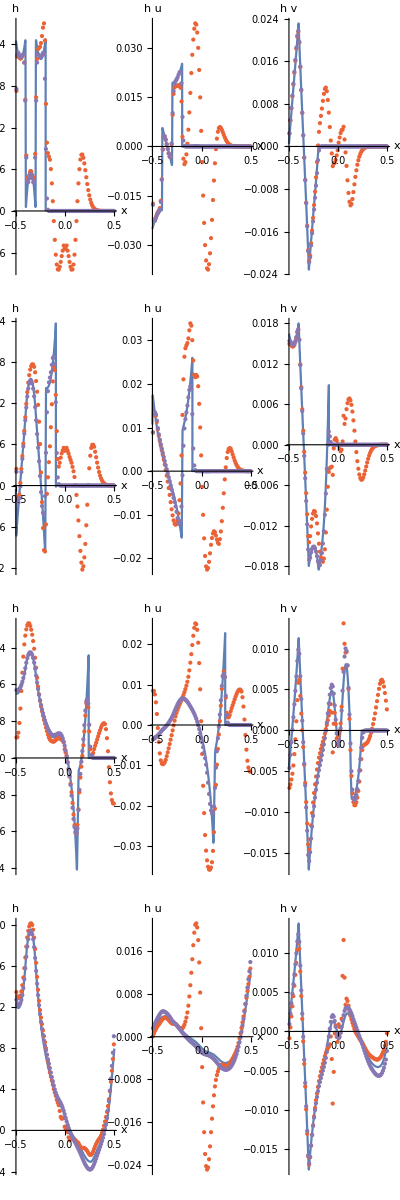

```mathematica
GraphicsGrid[#,ImageSize->1200]&/@List/@{
{
ListPlot[{Transpose[{qRef1[x],qRef1[h]-1-(0.5Exp[-128(qRef1[x]-0.00005)^2]+0.5Exp[-128(qRef1[x]+0.00005)^2])/2}],{{-10,0}},{{-10,0}},Transpose[{qRog1[x],qRog1[h]-(0.5Exp[-128(qUnb1[x]-0.005)^2]+0.5Exp[-128(qUnb1[x]+0.005)^2])/2}],Transpose[{qRogG1[x],qRogG1[h]}]},hOpts={AxesOrigin->{xlow,0},Joined->{True,False,False,False,False},PlotStyle->{,PointSize@Medium,PointSize@Medium,PointSize@Medium,PointSize@Medium},AxesLabel->{Style[x,Directive@14],Style[h,Directive@14]},TicksStyle->Directive[14],PlotRange->{{-.5,.5},All}}],
ListPlot[{Transpose[{qRef1[x],qRef1[hu]}],{{-10,0}},{{-10,0}},Transpose[{qRog1[x],qRog1[hu]}],Transpose[{qRogG1[x],qRogG1[hu]}]},huOpts={AxesOrigin->{xlow,0},Joined->{True,False,False,False,False},PlotStyle->{,PointSize@Medium,PointSize@Medium,PointSize@Medium,PointSize@Medium},AxesLabel->{Style[x,Directive@14],Style[h u,Directive@14]},TicksStyle->Directive[14],PlotRange->{{-.5,.5},All}}],
ListPlot[{Transpose[{qRef1[x],qRef1[hv]-500(0.5Exp[-128(qRef1[x]+0.00005)^2]-0.5Exp[-128(qRef1[x]-0.00005)^2])(2+0.5Exp[-128(qRef1[x]+0.00005)^2]+0.5Exp[-128(qRef1[x]-0.00005)^2])}],{{-10,0}},{{-10,0}},Transpose[{qRog1[x],qRog1[hv]-5(0.5Exp[-128(qRog1[x]+0.005)^2]-0.5Exp[-128(qRog1[x]-0.005)^2])(2+0.5Exp[-128(qRog1[x]+0.005)^2]+0.5Exp[-128(qRog1[x]-0.005)^2])}],Transpose[{qRogG1[x],qRogG1[hv]}]},hvOpts={AxesOrigin->{xlow,0},Joined->{True,False,False,False,False},PlotStyle->{,PointSize@Medium,PointSize@Medium,PointSize@Medium,PointSize@Medium},AxesLabel->{Style[x,Directive@14],Style[h v,Directive@14]},TicksStyle->Directive[14],PlotRange->{{-.5,.5},All}}]
},
{
ListPlot[{Transpose[{qRef1[x],qRef2[h]-1-(0.5Exp[-128(qRef1[x]-0.00005)^2]+0.5Exp[-128(qRef1[x]+0.00005)^2])/2}],{{-10,0}},{{-10,0}},Transpose[{qRog2[x],qRog2[h]-(0.5Exp[-128(qUnb1[x]-0.005)^2]+0.5Exp[-128(qUnb1[x]+0.005)^2])/2}],Transpose[{qRogG2[x],qRogG2[h]}]},hOpts],
ListPlot[{Transpose[{qRef2[x],qRef2[hu]}],{{-10,0}},{{-10,0}},Transpose[{qRog2[x],qRog2[hu]}],Transpose[{qRogG2[x],qRogG2[hu]}]},huOpts],
ListPlot[{Transpose[{qRef2[x],qRef2[hv]-500(0.5Exp[-128(qRef1[x]+0.00005)^2]-0.5Exp[-128(qRef1[x]-0.00005)^2])(2+0.5Exp[-128(qRef1[x]+0.00005)^2]+0.5Exp[-128(qRef1[x]-0.00005)^2])}],{{-10,0}},{{-10,0}},Transpose[{qRog2[x],qRog2[hv]-5(0.5Exp[-128(qRog1[x]+0.005)^2]-0.5Exp[-128(qRog1[x]-0.005)^2])(2+0.5Exp[-128(qRog1[x]+0.005)^2]+0.5Exp[-128(qRog1[x]-0.005)^2])}],Transpose[{qRogG2[x],qRogG2[hv]}]},hvOpts]
},
{
ListPlot[{Transpose[{qRef1[x],qRef5[h]-1-(0.5Exp[-128(qRef1[x]-0.00005)^2]+0.5Exp[-128(qRef1[x]+0.00005)^2])/2}],{{-10,0}},{{-10,0}},Transpose[{qRog5[x],qRog5[h]-(0.5Exp[-128(qUnb1[x]-0.005)^2]+0.5Exp[-128(qUnb1[x]+0.005)^2])/2}],Transpose[{qRogG5[x],qRogG5[h]}]},hOpts],
ListPlot[{Transpose[{qRef5[x],qRef5[hu]}],{{-10,0}},{{-10,0}},Transpose[{qRog5[x],qRog5[hu]}],Transpose[{qRogG5[x],qRogG5[hu]}]},huOpts],
ListPlot[{Transpose[{qRef5[x],qRef5[hv]-500(0.5Exp[-128(qRef1[x]+0.00005)^2]-0.5Exp[-128(qRef1[x]-0.00005)^2])(2+0.5Exp[-128(qRef1[x]+0.00005)^2]+0.5Exp[-128(qRef1[x]-0.00005)^2])}],{{-10,0}},{{-10,0}},Transpose[{qRog5[x],qRog5[hv]-5(0.5Exp[-128(qRog1[x]+0.005)^2]-0.5Exp[-128(qRog1[x]-0.005)^2])(2+0.5Exp[-128(qRog1[x]+0.005)^2]+0.5Exp[-128(qRog1[x]-0.005)^2])}],Transpose[{qRogG5[x],qRogG5[hv]}]},hvOpts]
},
{
ListPlot[{Transpose[{qRef1[x],qRef10[h]-1-(0.5Exp[-128(qRef1[x]-0.00005)^2]+0.5Exp[-128(qRef1[x]+0.00005)^2])/2}],{{-10,0}},{{-10,0}},Transpose[{qRog10[x],qRog10[h]-(0.5Exp[-128(qUnb1[x]-0.005)^2]+0.5Exp[-128(qUnb1[x]+0.005)^2])/2}],Transpose[{qRogG10[x],qRogG10[h]}]},hOpts],
ListPlot[{Transpose[{qRef10[x],qRef10[hu]}],{{-10,0}},{{-10,0}},Transpose[{qRog10[x],qRog10[hu]}],Transpose[{qRogG10[x],qRogG10[hu]}]},huOpts],
ListPlot[{Transpose[{qRef10[x],qRef10[hv]-500(0.5Exp[-128(qRef1[x]+0.00005)^2]-0.5Exp[-128(qRef1[x]-0.00005)^2])(2+0.5Exp[-128(qRef1[x]+0.00005)^2]+0.5Exp[-128(qRef1[x]-0.00005)^2])}],{{-10,0}},{{-10,0}},Transpose[{qRog10[x],qRog10[hv]-5(0.5Exp[-128(qRog1[x]+0.005)^2]-0.5Exp[-128(qRog1[x]-0.005)^2])(2+0.5Exp[-128(qRog1[x]+0.005)^2]+0.5Exp[-128(qRog1[x]-0.005)^2])}],Transpose[{qRogG10[x],qRogG10[hv]}]},hvOpts]
}
}//TableForm
```

```mathematica
5(0.5Exp[-128(qUnb1[x]+0.005)^2]-0.5Exp[-128(qUnb1[x]-0.005)^2])(2+0.5Exp[-128(qUnb1[x]+0.005)^2]+0.5Exp[-128(qUnb1[x]-0.005)^2])
```

{1.61525×10^-13,5.53378×10^-13,1.84724×10^-12,6.00811×10^-12,1.90395×10^-11,5.8785×10^-11,1.76833×10^-10,5.18244×10^-10,1.47968×10^-9,4.11582×10^-9,1.11528×10^-8,2.94399×10^-8,7.5701×10^-8,1.8961×10^-7,4.62595×10^-7,1.09926×10^-6,2.54413×10^-6,5.73452×10^-6,0.0000125878,0.0000269071,0.0000560047,0.000113498,0.000223938,0.000430135,0.00080423,0.00146357,0.00259221,0.00446794,0.00749373,0.0122299,0.019421,0.0300097,0.0451264,0.0660437,0.0940872,0.130492,0.176198,0.231576,0.296083,0.367856,0.443286,0.516681,0.5802,0.624262,0.638614,0.614085,0.544763,0.430069,0.276035,0.095186,-0.095186,-0.276035,-0.430069,-0.544763,-0.614085,-0.638614,-0.624262,-0.5802,-0.516681,-0.443286,-0.367856,-0.296083,-0.231576,-0.176198,-0.130492,-0.0940872,-0.0660437,-0.0451264,-0.0300097,-0.019421,-0.0122299,-0.00749373,-0.00446794,-0.00259221,-0.00146357,-0.00080423,-0.000430135,-0.000223938,-0.000113498,-0.0000560047,-0.0000269071,-0.0000125878,-5.73452×10^-6,-2.54413×10^-6,-1.09926×10^-6,-4.62595×10^-7,-1.8961×10^-7,-7.5701×10^-8,-2.94399×10^-8,-1.11528×10^-8,-4.11582×10^-9,-1.47968×10^-9,-5.18244×10^-10,-1.76833×10^-10,-5.8785×10^-11,-1.90395×10^-11,-6.00811×10^-12,-1.84724×10^-12,-5.53378×10^-13,-1.61525×10^-13}